```mathematica
(* TECHNOLOGY PARAMETER FITTING *)

(* Clear everything *)
ClearAll["Global`*"]

(* Parameters: modify for each technology *)
techAParams={ρ->0.3*10^-6,Lmax->4*10^-9,wmax->50*10^-9,LT->1*10^-9,w0->0.5*10^-9,Rpar->2000,VT->0.4,I0->5*10^14,Ea1->1.2,Ea2->1.2,kT->0.026,gmax->240*10^-6,γ->10^6,w1->1*10^-10,w2->1*10^-9};
techBParams={ρ->0.3*10^-6,Lmax->3*10^-9,wmax->50*10^-9,LT->0.5*10^-9,w0->0.5*10^-9,Rpar->5000,VT->0.4,I0->5*10^14,Ea1->1.2,Ea2->1.2,kT->0.026,gmax->128*10^-6,γ->10^6,w1->1*10^-10,w2->1*10^-9};
techCParams={ρ->8*10^-6,LT->0.4*10^-9,Rpar->10000,VT->0.4,I0->5*10^12,Ea1->1.2,Ea2->1.6,γ->10^9,d1->0.5*10^-9,d2->5*10^-9, ρL->0.25*10^-18,ρA->0.5*10^-9, tau0->1,Lmax->8*10^-9,w0->0.5*10^-9,gmax->40*10^-6,fs->10^6,kT->0.026};
subs=techCParams;

(* Functions for conductance as a function of length and area in Stages 1 and 2 *)
g[A_,L_]:=(VT/(I0 A ⅇ^(-(Lmax-L)/LT))+(ρ L)/A+Rpar)^-1
gs1[L_]:=g[A0,L]
gs2[A_]:=g[A,Lmax]
```

1.2

```mathematica
Plot3D[g[A/10^18,Lmax-gap/10^9/.subs]*10^6/.subs,{gap,0/.subs,Lmax/4*10^9/.subs},{A,w0^2*10^18/.subs,16}, PlotLegends->Automatic,AxesLabel->{"Gap (nm)", "Area (nm^2)", "Cond. (µS) "},PlotLabel->"Conductance 3D Plot (µS)",ImageSize->300,PlotRange->All]
```

-Graphics3D-

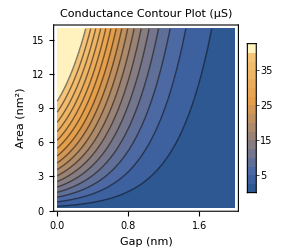

```mathematica
ContourPlot[g[A/10^18,Lmax-gap/10^9/.subs]*10^6/.subs,{gap,0/.subs,Lmax/4*10^9/.subs},{A,w0^2*10^18/.subs,16}, PlotLegends->Automatic,Contours->Range[0,40,40/16], FrameLabel->{"Gap (nm)", "Area (nm^2)"},PlotLabel->"Conductance Contour Plot (µS)",ImageSize->250,PlotRange->All]
```

(g (ⅇ^((-L+Lmax)/LT) VT+I0 L ρ))/(I0-g I0 Rpar)

(A-A g Rpar+g LT ρ ProductLog[-1,-(ⅇ^((A (-1+g Rpar)+g Lmax ρ)/(g LT ρ)) VT)/(I0 LT ρ)])/(g ρ)

General::munfl: Exp[-6.11881×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6048.88] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2990.97] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

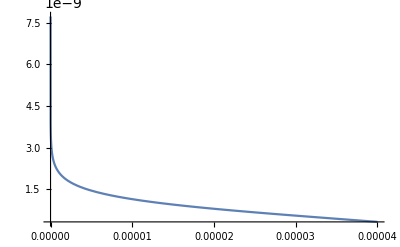

```mathematica
(* Now what we want to do is integrate over the contour to get a distribution *)
Off[Solve::ifun]
W[x_]:=ProductLog[-1,x]
AofLg=FullSimplify[A/.Solve[g[A,L]==g, A]][[1]]
LofAg=FullSimplify[L/.Solve[g[A,L]==g, L]][[1]]/.{ProductLog->W}
Plot[Lmax-LofAg/.Rationalize[subs] /.{A->16*10^-18},{g,0,40*10^-6}, PlotRange->All,WorkingPrecision->100]
```

NormalDistribution[0,1]

LogNormalDistribution[0,1]

0.01

39.8942 ⅇ^(-5000. (-5+L)^2)

p[L,0]==39.8942 ⅇ^(-5000. (-5+L)^2)

General::munfl: Exp[-124990.] is too small to represent as a normalized machine number; precision may be lost.

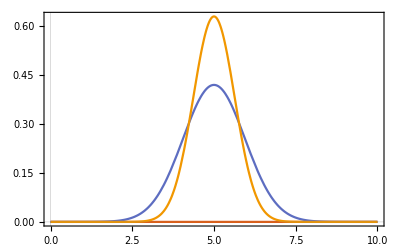

General::munfl: Exp[-124990.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-114994.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-105415.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

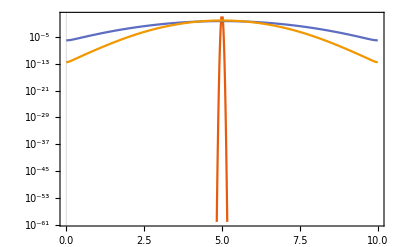

```mathematica
test=NormalDistribution[]
test2=TransformedDistribution[Exp[x],x\[Distributed]test]
```

```mathematica
td = TransformedDistribution[1/(A*L)g[A,L]/.{A->(g (ⅇ^((-L+Lmax)/LT) VT+I0 L ρ))/(I0-g I0 Rpar)/.{g->15*10^-6}}/.{L->Lmax-gap}/.subs, gap\[Distributed]NormalDistribution[0.6*10^-9,0.2*10^-9 ]]
Plot[PDF[SmoothKernelDistribution[RandomVariate[td, 100000],MaxMixtureKernels->All]][x],{x,1*^19,1*^21}]
```

TransformedDistribution[(200000 (I0-(3 I0 Rpar)/200000))/(3 (-x+Lmax) (ⅇ^(x/LT) VT+I0 (-x+Lmax) ρ) (Rpar+(200000 ⅇ^(x/LT) (I0-(3 I0 Rpar)/200000) VT)/(3 I0 (ⅇ^(x/LT) VT+I0 (-x+Lmax) ρ))+(200000 (-x+Lmax) (I0-(3 I0 Rpar)/200000) ρ)/(3 (ⅇ^(x/LT) VT+I0 (-x+Lmax) ρ)))),x\[Distributed]NormalDistribution[6.×10^-10,2.×10^-10]]

TransformedDistribution::nnbprm: The valid numeric parameters of distribution TransformedDistribution[(200000 (I0-(3 I0 Rpar)/200000))/(3 (-x+Lmax) (ⅇ^(x Power[«2»]) VT+I0 (-x+Lmax) ρ) (Rpar+(200000 ⅇ^(x Power[«2»]) (I0-(3 I0 Rpar)/200000) VT)/(3 I0 (Times[«2»]+Times[«3»]))+(200000 (-x+Lmax) (I0-(3 I0 Rpar)/200000) ρ)/(3 (Times[«2»]+Times[«3»])))),x\[Distributed]NormalDistribution[6.×10^-10,2.×10^-10]] are expected. Use DistributionParameterAssumptions to obtain the parameter assumptions.

SmoothKernelDistribution::invldd: The input data SmoothKernelDistribution[RandomVariate[TransformedDistribution[(200000 (I0-(3 I0 Rpar)/200000))/(3 (-x+Lmax) (Power[«2»] VT+I0 Plus[«2»] ρ) (Rpar+200000/3 Power[«2»] Power[«2»] Plus[«2»] VT Power[«2»]+200000/3 Plus[«2»] Plus[«2»] ρ Power[«2»])),x\[Distributed]NormalDistribution[6.×10^-10,2.×10^-10]],100000]] should be a vector or a matrix of real numbers or a valid TemporalData object.

TransformedDistribution::nnbprm: The valid numeric parameters of distribution TransformedDistribution[(66666.7 (I0-0.000015 I0 Rpar))/((-1. x+Lmax) (2.71828^(x Power[«2»]) VT+I0 (-1. x+Lmax) ρ) (Rpar+(66666.7 2.71828^(x Power[«2»]) (I0-0.000015 I0 Rpar) VT)/(I0 (Times[«2»]+Times[«3»]))+(66666.7 (-1. x+Lmax) (I0-0.000015 I0 Rpar) ρ)/(Times[«2»]+Times[«3»]))),x\[Distributed]NormalDistribution[6.×10^-10,2.×10^-10]] are expected. Use DistributionParameterAssumptions to obtain the parameter assumptions.

SmoothKernelDistribution::invldd: The input data SmoothKernelDistribution[RandomVariate[TransformedDistribution[(66666.7 (I0-0.000015 I0 Rpar))/((-1. x+Lmax) (Power[«2»] VT+I0 Plus[«2»] ρ) (Rpar+66666.7 Power[«2»] Power[«2»] Plus[«2»] VT Power[«2»]+66666.7 Plus[«2»] Plus[«2»] ρ Power[«2»])),x\[Distributed]NormalDistribution[6.×10^-10,2.×10^-10]],100000.]] should be a vector or a matrix of real numbers or a valid TemporalData object.

TransformedDistribution::nnbprm: The valid numeric parameters of distribution TransformedDistribution[(200000 (I0-(3 I0 Rpar)/200000))/(3 (-x+Lmax) (ⅇ^(x Power[«2»]) VT+I0 (-x+Lmax) ρ) (Rpar+(200000 ⅇ^(x Power[«2»]) (I0-(3 I0 Rpar)/200000) VT)/(3 I0 (Times[«2»]+Times[«3»]))+(200000 (-x+Lmax) (I0-(3 I0 Rpar)/200000) ρ)/(3 (Times[«2»]+Times[«3»])))),x\[Distributed]NormalDistribution[6.×10^-10,2.×10^-10]] are expected. Use DistributionParameterAssumptions to obtain the parameter assumptions.

General::stop: Further output of TransformedDistribution::nnbprm will be suppressed during this calculation.

SmoothKernelDistribution::invldd: The input data SmoothKernelDistribution[RandomVariate[TransformedDistribution[(200000 (I0-(3 I0 Rpar)/200000))/(3 (-x+Lmax) (Power[«2»] VT+I0 Plus[«2»] ρ) (Rpar+200000/3 Power[«2»] Power[«2»] Plus[«2»] VT Power[«2»]+200000/3 Plus[«2»] Plus[«2»] ρ Power[«2»])),x\[Distributed]NormalDistribution[6.×10^-10,2.×10^-10]],100000]] should be a vector or a matrix of real numbers or a valid TemporalData object.

General::stop: Further output of SmoothKernelDistribution::invldd will be suppressed during this calculation.

-Graphics-

```mathematica
tf=0.01
icfn=PDF[NormalDistribution[5,0.01]][L]
ic=p[L,0]==icfn
method={"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.001}}}};
heqn=D[p[L,t],t]-Integrate[D[ p[L,t],{L,2}]*σ^2/2*PDF[LogNormalDistribution[0,1.5]][σ],{σ,0,∞}]==NeumannValue[0,L==0]+NeumannValue[0,L==10];
heqnorig=D[p[L,t],t]-D[20p[L,t],{L,2}]==NeumannValue[0,L==0]+NeumannValue[0,L==10];
Lfpdf=p[L,tf]/.NDSolve[{heqn,ic},p[L,tf],{L,0,10},{t,0,tf},InterpolationOrder->All,Method->method];
Lfpdf2=p[L,tf]/.NDSolve[{heqnorig,ic},p[L,tf],{L,0,10},{t,0,tf},InterpolationOrder->All,Method->method];
Plot[{icfn,Lfpdf, Lfpdf2},{L,0,10},PlotRange->All,PlotTheme->"Scientific"]
LogPlot[{icfn,Lfpdf, Lfpdf2},{L,0,10},PlotRange->{10^-60,10},PlotTheme->"Scientific"]
```